```mathematica
ndist:=NormalDistribution[0,1];
Phi[x_]:=CDF[ndist,x] ;
Psi[t_,x_]:=PDF[LogNormalDistribution[muc*t,Sc*Sqrt[t]],x] ;
(* ####################### To Define by the user #######################  *)
(* Parametrs to define *)

mu:=1;Sc:=2;

(*Define the estimated distribution *)

TTarg[x_] :=CDF[ExponentialDistribution[0.5],x];

(* ####################### *)

muc:=mu-0.5Sc^2
Targ[x_] := TTarg'[x] ;

G[x_?NumberQ]:=NIntegrate[TTarg[y]-0.5,{y,0,x}] ;
H[x_]:= 0.5*mu*x*(2*TTarg[x]-1)+0.5*Sc^2*x^2*Targ[x];

(*Find the median of F*)
mm := x/.FindRoot[TTarg[x]==0.5,{x,1}] ;
Print[mm]
(*Find alpha or beta : zero of the function H*)
FindRoot[H[y]==0,{y,mm}]


(*##### Verefy #####*)

mu := 1 ;S:= 2;
Manipulate[Plot[{x*Targ[x],mu/(S^2/2)(1/2-TTarg[x])},{x,0,10},PlotRange->{-1,5}],{S,0.001,2},{mu,0.01,2}] 
Dynamic[MousePosition["Graphics"]]
```

1.38629

{y→0.391798}

```mathematica
Plot[{H[x]},{x,1000,3000}]
```

```mathematica
(* EEG --> Function J in the papaer*)

EEG[x_?NumberQ,t_?NumberQ]:=NIntegrate[G[x*y]*Psi[T-t,y],{y,0,Infinity}];

(* EEH --> function K in the paper  *)

EEH[x_?NumberQ,t_?NumberQ,y_?NumberQ]:=NIntegrate[H[x*z]*Psi[t,z],{z,y/x,Infinity}];

(*Function L in the paper *)
EEL[x_,t_,y_] := NIntegrate[H[x*z]*Psi[t,z],{z,0,y/x}];
(*Integral Of L *)

INTEEL[x_,t_] :=h Sum[EEL[x,k h,bb[t+k h]],{k,1,NN-IntegerPart[t/h]}];

(*Integral of K *)

INTEEH[x_?NumberQ,t_?NumberQ]:=h Sum[EEH[x,k h,bb[t+k h]],{k,1,NN-IntegerPart[t/h]}];


(* #######  In the case of mu < 0 ,change INTEEH into INTEEL in the follwoing part of code *) 
loc =0.4  ;(*Where Mathemaica will search the zeros, between alpha and m*)

dd:=x/.FindRoot[H[x]==0,{x,mm}];

Print[dd];

(*##### Parameters ######*)

T=1;Clear[bb];bb[T]=dd;NN=100;h=T/NN;

bb[(NN-1)h]=x/.FindRoot[G[x]==EEG[x,(NN-1)h]-INTEEH[x,(NN-1)h],{x,mm}];

Print[bb[(NN-1)h]];


For[k=2, k<NN+1, k++,bb[(NN-k)h]=x/.FindRoot[G[x]==EEG[x,(NN-k)h]-INTEEH[x,(NN-k)h],{x,loc}];
(*Print[bb[T]];*)
Print[bb[(NN-k)h]];
];
```

0.391798

2.21996

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.415193

0.421825

0.429513

0.436989

0.444164

1.29719

1.66824

2.12089

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

1.24646

1.24999

1.25311

1.25626

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.60004}. NIntegrate obtained 1.79093 and 0.000136865 for the integral and error estimates.

bb[h (-k+NN)]

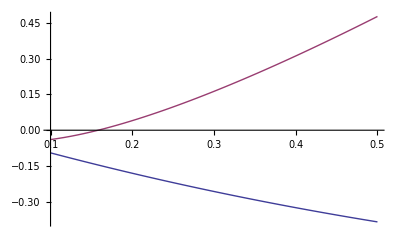

```mathematica
Plot[{G[x],EEG[x,h]-h EEH[x,h,dd]},{x,0.1,0.5},PlotRange->All]
```

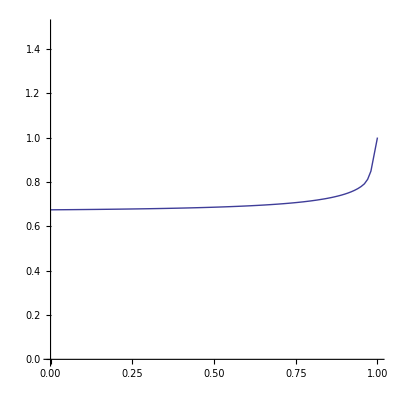

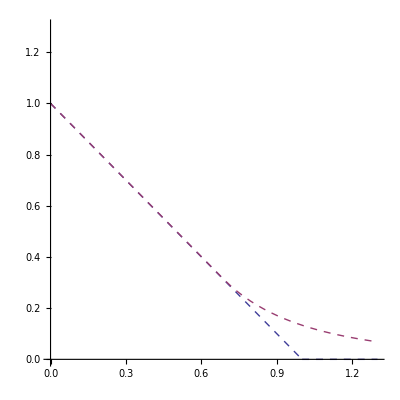

```mathematica
Do[bbA[(NN-k)h]=x/.FindRoot[FFA[(NN-k)h,x]==GGA[(NN-k)h,x],{x,bbA[(NN-k+1)h]+eps}],{k,1,NN}];
bbA[T-h] = (bbA[T-2h]+bbA[T])/2;
bbA=Interpolation[Table[{k h,bbA[k h]},{k,0,NN}],InterpolationOrder->1];
Plot[bbA[x],{x,0,T},PlotRange->{0,K+K/2},AspectRatio->1]

VVVA[t_?NumberQ,x_?NumberQ]:=Exp[-r(T-t)](K Phi[1/(S Sqrt[T-t])(Log[K/x]-(r-S^2/2)(T-t))]-x Exp[r(T-t)] Phi[1/(S Sqrt[T-t]) (Log[K/x]-(r+S^2/2)(T-t))])+NIntegrate[KKKKKA[t,x,v,bbA[v]],{v,t,T}]
Plot[{Max[K-x,0],VVVA[0.5,x]},{x,0,1.3},PlotRange->{0,1.3},AspectRatio->1,PlotStyle->{Dashed}]
```